```mathematica
m1=10000;
tend = 200;
numberLmodes=6;
tails[i_,data_, LmodePosition_,GridePosition_]:=i*((Re[data[[1,LmodePosition,(m1/tend)*i,GridePosition]]]*Re[data[[2,LmodePosition,(m1/tend)*i,GridePosition]]]  + Im[data[[1,LmodePosition,(m1/tend)*i,GridePosition]]]*Im[data[[2,LmodePosition,(m1/tend)*i,GridePosition]]])/(Re[data[[1,LmodePosition,(m1/tend)*i,GridePosition]]]^2 + Im[data[[1,LmodePosition,(m1/tend)*i,GridePosition]]]^2))
```

Schwarzschild

S=0

σ ψ_0[τ,σ]+σ (-2+3 σ) ψ_0^(0,1)[τ,σ]+(-1+σ) σ^2 ψ_0^(0,2)[τ,σ]+2 σ ψ_0^(1,0)[τ,σ]+(-1+2 σ^2) ψ_0^(1,1)[τ,σ]+(1+σ) ψ_0^(2,0)[τ,σ] (L=0) 
(2+σ) ψ_1[τ,σ]+σ (-2+3 σ) ψ_1^(0,1)[τ,σ]+(-1+σ) σ^2 ψ_1^(0,2)[τ,σ]+2 σ ψ_1^(1,0)[τ,σ]+(-1+2 σ^2) ψ_1^(1,1)[τ,σ]+(1+σ) ψ_1^(2,0)[τ,σ] (L=1)
(6+σ) ψ_2[τ,σ]+σ (-2+3 σ) ψ_2^(0,1)[τ,σ]+(-1+σ) σ^2 ψ_2^(0,2)[τ,σ]+2 σ ψ_2^(1,0)[τ,σ]+(-1+2 σ^2) ψ_2^(1,1)[τ,σ]+(1+σ) ψ_2^(2,0)[τ,σ] (L=2)
(12+σ) ψ_3[τ,σ]+σ (-2+3 σ) ψ_3^(0,1)[τ,σ]+(-1+σ) σ^2 ψ_3^(0,2)[τ,σ]+2 σ ψ_3^(1,0)[τ,σ]+(-1+2 σ^2) ψ_3^(1,1)[τ,σ]+(1+σ) ψ_3^(2,0)[τ,σ](L=3)

```mathematica
s0 = Import["C:\\Users\\brays\\PHD_CodeWork\\Data\\Schwar\\S=0.m.gz"];
```

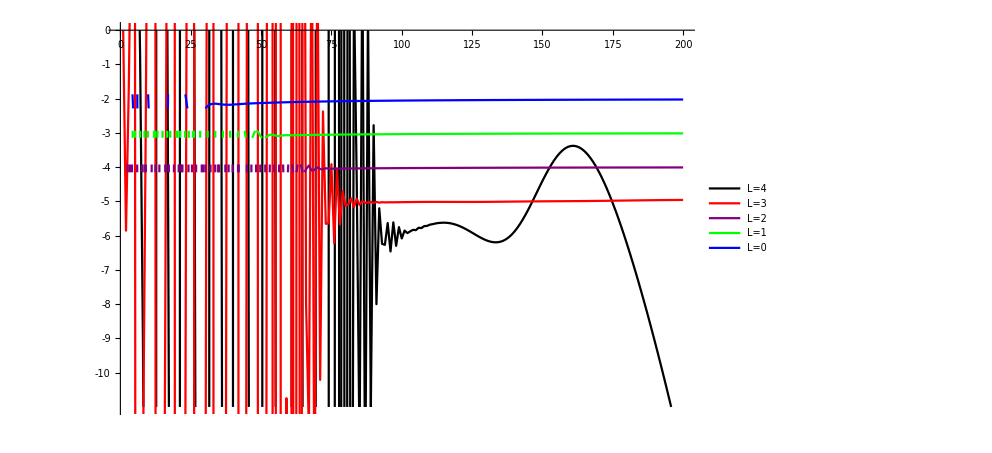

```mathematica
GridePosition=1;
listRepeatedS0=Table[ ConstantArray[0,tend],numberLmodes];
Do[
Do[listRepeatedS0[[j]][[i]]=tails[i,s0,j,GridePosition],
{i,2,tend}], {j,1,numberLmodes}
]
ListPlot[listRepeatedS0[[1]],Joined->True, PlotStyle->Blue, PlotLegends->{"L=0"}];
ListPlot[listRepeatedS0[[2]],Joined->True, PlotStyle->Green, PlotLegends->{"L=1"}];
ListPlot[listRepeatedS0[[3]],Joined->True, PlotStyle->Purple, PlotLegends->{"L=2"}];
ListPlot[listRepeatedS0[[4]],Joined->True, PlotStyle->Red, PlotLegends->{"L=3"}];
ListPlot[listRepeatedS0[[5]],Joined->True, PlotStyle->Black,PlotRange->{0,-11}, PlotLegends->{"L=4"},Ticks->{ Automatic,-Range[0,10,1]}];
Show[%,%%,%%%, %%%%, %%%%%]
```

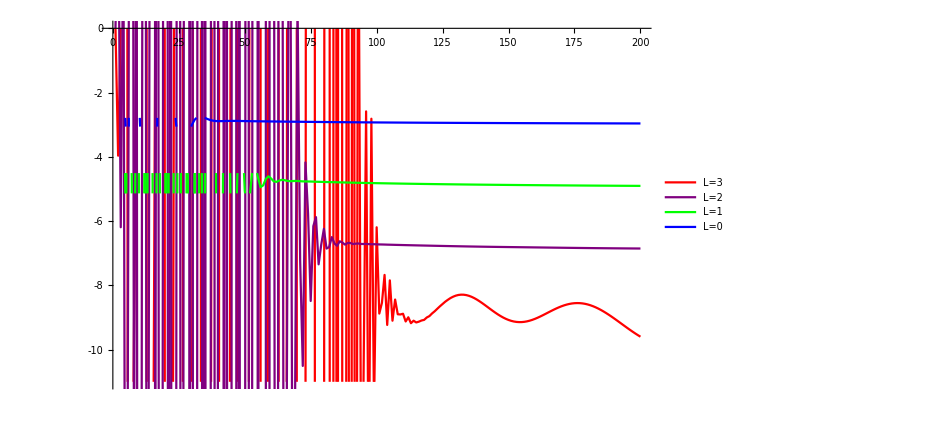

```mathematica
GridePosition=50;
listRepeatedS0=Table[ ConstantArray[0,tend],numberLmodes];
Do[
Do[listRepeatedS0[[j]][[i]]=tails[i,s0,j,GridePosition],
{i,2,tend}], {j,1,numberLmodes}
]
ListPlot[listRepeatedS0[[1]],Joined->True, PlotStyle->Blue, PlotLegends->{"L=0"}];
ListPlot[listRepeatedS0[[2]],Joined->True, PlotStyle->Green, PlotLegends->{"L=1"}];
ListPlot[listRepeatedS0[[3]],Joined->True, PlotStyle->Purple, PlotLegends->{"L=2"}];
ListPlot[listRepeatedS0[[4]],Joined->True, PlotStyle->Red,PlotRange->{0,-11}, PlotLegends->{"L=3"},Ticks->{ Automatic,-Range[0,10,1]}];
Show[%,%%,%%%, %%%%]
```

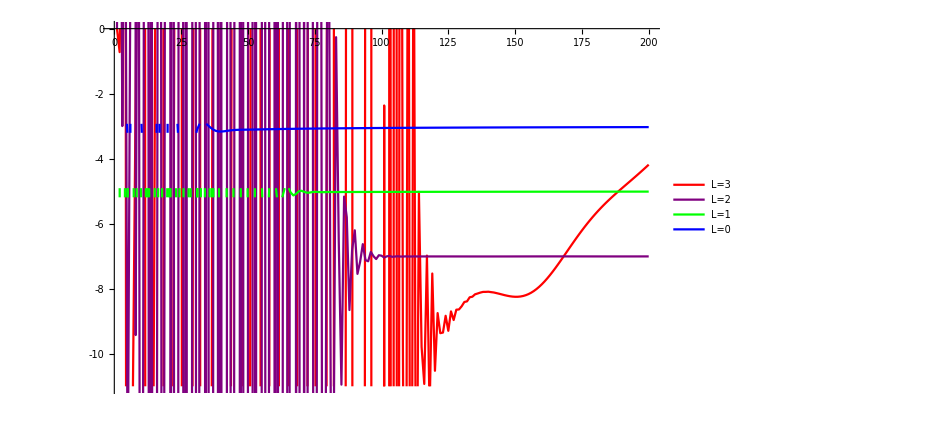

```mathematica
GridePosition=100;
listRepeatedS0=Table[ ConstantArray[0,tend],numberLmodes];
Do[
Do[listRepeatedS0[[j]][[i]]=tails[i,s0,j,GridePosition],
{i,2,tend}], {j,1,numberLmodes}
]
ListPlot[listRepeatedS0[[1]],Joined->True, PlotStyle->Blue, PlotLegends->{"L=0"}];
ListPlot[listRepeatedS0[[2]],Joined->True, PlotStyle->Green, PlotLegends->{"L=1"}];
ListPlot[listRepeatedS0[[3]],Joined->True, PlotStyle->Purple, PlotLegends->{"L=2"}];
ListPlot[listRepeatedS0[[4]],Joined->True, PlotStyle->Red,PlotRange->{0,-11}, PlotLegends->{"L=3"},Ticks->{ Automatic,-Range[0,10,1]}];
Show[%,%%,%%%, %%%%]
```

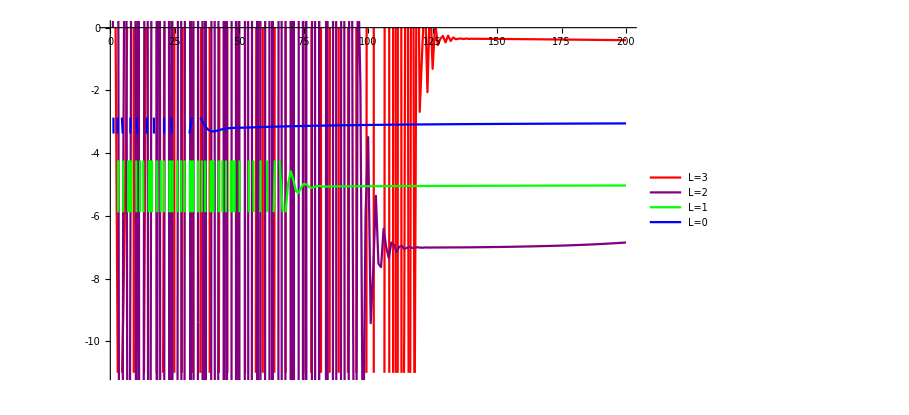

```mathematica
GridePosition=256;
listRepeatedS0=Table[ ConstantArray[0,tend],numberLmodes];
Do[
Do[listRepeatedS0[[j]][[i]]=tails[i,s0,j,GridePosition],
{i,2,tend}], {j,1,numberLmodes}
]
ListPlot[listRepeatedS0[[1]],Joined->True, PlotStyle->Blue, PlotLegends->{"L=0"}];
ListPlot[listRepeatedS0[[2]],Joined->True, PlotStyle->Green, PlotLegends->{"L=1"}];
ListPlot[listRepeatedS0[[3]],Joined->True, PlotStyle->Purple, PlotLegends->{"L=2"}];
ListPlot[listRepeatedS0[[4]],Joined->True, PlotStyle->Red,PlotRange->{0,-11}, PlotLegends->{"L=3"},Ticks->{ Automatic,-Range[0,10,1]}];
Show[%,%%,%%%, %%%%]
```

S=1

2 σ ψ_1[τ,σ]+σ (-4+4 σ) ψ_1^(0,1)[τ,σ]+(-1+σ) σ^2 ψ_1^(0,2)[τ,σ]+(-1+3 σ) ψ_1^(1,0)[τ,σ]+(-1+2 σ^2) ψ_1^(1,1)[τ,σ]+(1+σ) ψ_1^(2,0)[τ,σ] 
(4+2 σ) ψ_2[τ,σ]+σ (-4+4 σ) ψ_2^(0,1)[τ,σ]+(-1+σ) σ^2 ψ_2^(0,2)[τ,σ]+(-1+3 σ) ψ_2^(1,0)[τ,σ]+(-1+2 σ^2) ψ_2^(1,1)[τ,σ]+(1+σ) ψ_2^(2,0)[τ,σ]
(10+2 σ) ψ_3[τ,σ]+σ (-4+4 σ) ψ_3^(0,1)[τ,σ]+(-1+σ) σ^2 ψ_3^(0,2)[τ,σ]+(-1+3 σ) ψ_3^(1,0)[τ,σ]+(-1+2 σ^2) ψ_3^(1,1)[τ,σ]+(1+σ) ψ_3^(2,0)[τ,σ]
(18+2 σ) ψ_4[τ,σ]+σ (-4+4 σ) ψ_4^(0,1)[τ,σ]+(-1+σ) σ^2 ψ_4^(0,2)[τ,σ]+(-1+3 σ) ψ_4^(1,0)[τ,σ]+(-1+2 σ^2) ψ_4^(1,1)[τ,σ]+(1+σ) ψ_4^(2,0)[τ,σ]

```mathematica
s1 = Import["C:\\Users\\brays\\PHD_CodeWork\\Data\\Schwar\\S=1.m.gz"];
```

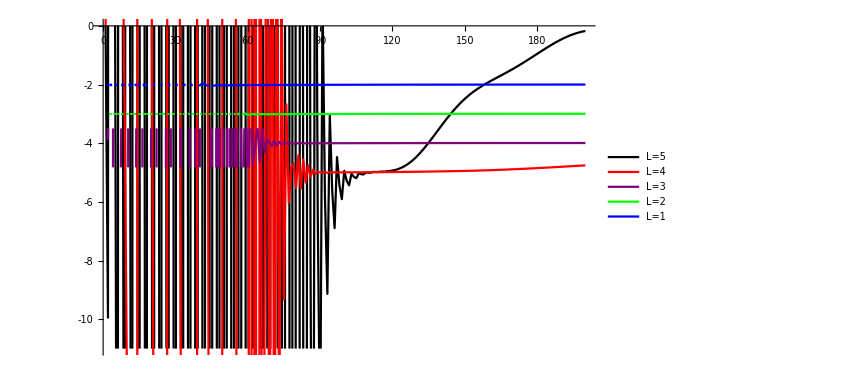

```mathematica
GridePosition=1;
listRepeatedS1=Table[ ConstantArray[0,tend],numberLmodes];
Do[
Do[listRepeatedS1[[j]][[i]]=tails[i,s1,j,GridePosition],
{i,2,tend}], {j,1,numberLmodes}
]
ListPlot[listRepeatedS1[[1]],Joined->True, PlotStyle->Blue, PlotLegends->{"L=1"}];
ListPlot[listRepeatedS1[[2]],Joined->True, PlotStyle->Green, PlotLegends->{"L=2"}];
ListPlot[listRepeatedS1[[3]],Joined->True, PlotStyle->Purple, PlotLegends->{"L=3"}];
ListPlot[listRepeatedS1[[4]],Joined->True, PlotStyle->Red, PlotLegends->{"L=4"}];
ListPlot[listRepeatedS1[[5]],Joined->True, PlotStyle->Black,PlotRange->{0,-11}, PlotLegends->{"L=5"},Ticks->{ Automatic,-Range[0,10,1]}];
Show[%,%%,%%%, %%%%,%%%%%]
```

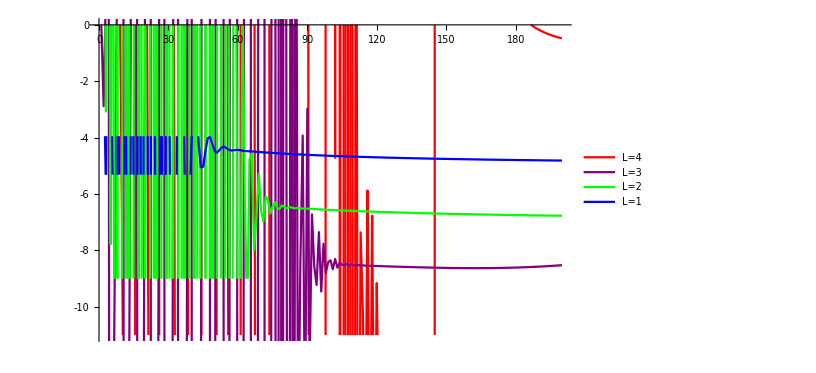

```mathematica
GridePosition=50;
listRepeatedS1=Table[ ConstantArray[0,tend],numberLmodes];
Do[
Do[listRepeatedS1[[j]][[i]]=tails[i,s1,j,GridePosition],
{i,2,tend}], {j,1,numberLmodes}
]
ListPlot[listRepeatedS1[[1]],Joined->True, PlotStyle->Blue, PlotLegends->{"L=1"}];
ListPlot[listRepeatedS1[[2]],Joined->True, PlotStyle->Green, PlotLegends->{"L=2"}];
ListPlot[listRepeatedS1[[3]],Joined->True, PlotStyle->Purple, PlotLegends->{"L=3"}];
ListPlot[listRepeatedS1[[4]],Joined->True, PlotStyle->Red,PlotRange->{0,-11}, PlotLegends->{"L=4"},Ticks->{ Automatic,-Range[0,10,1]}];
Show[%,%%,%%%, %%%%]
```

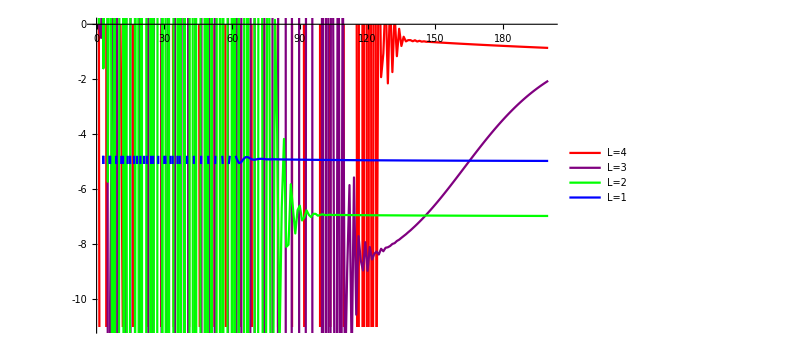

```mathematica
GridePosition=100;
listRepeatedS1=Table[ ConstantArray[0,tend],numberLmodes];
Do[
Do[listRepeatedS1[[j]][[i]]=tails[i,s1,j,GridePosition],
{i,2,tend}], {j,1,numberLmodes}
]
ListPlot[listRepeatedS1[[1]],Joined->True, PlotStyle->Blue, PlotLegends->{"L=1"}];
ListPlot[listRepeatedS1[[2]],Joined->True, PlotStyle->Green, PlotLegends->{"L=2"}];
ListPlot[listRepeatedS1[[3]],Joined->True, PlotStyle->Purple, PlotLegends->{"L=3"}];
ListPlot[listRepeatedS1[[4]],Joined->True, PlotStyle->Red,PlotRange->{0,-11}, PlotLegends->{"L=4"},Ticks->{ Automatic,-Range[0,10,1]}];
Show[%,%%,%%%, %%%%]
```

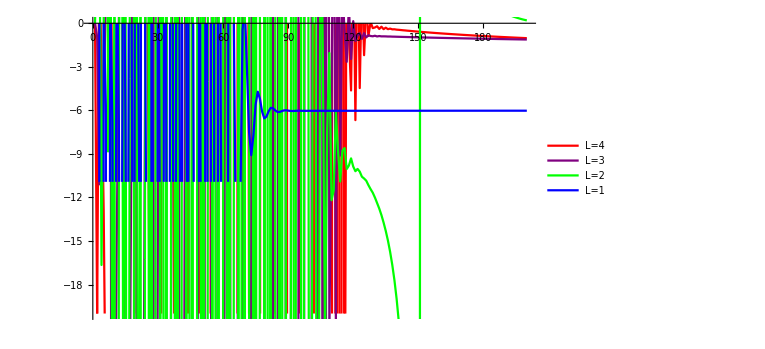

```mathematica
GridePosition=256;
listRepeatedS1=Table[ ConstantArray[0,tend],numberLmodes];
Do[
Do[listRepeatedS1[[j]][[i]]=tails[i,s1,j,GridePosition],
{i,2,tend}], {j,1,numberLmodes}
]
ListPlot[listRepeatedS1[[1]],Joined->True, PlotStyle->Blue, PlotLegends->{"L=1"}];
ListPlot[listRepeatedS1[[2]],Joined->True, PlotStyle->Green, PlotLegends->{"L=2"}];
ListPlot[listRepeatedS1[[3]],Joined->True, PlotStyle->Purple, PlotLegends->{"L=3"}];
ListPlot[listRepeatedS1[[4]],Joined->True, PlotStyle->Red,PlotRange->{0,-20}, PlotLegends->{"L=4"}];
Show[%,%%,%%%, %%%%]
```

```mathematica
S=2
```

3 σ ψ_2[τ,σ]+σ (-2+2 (-2+σ)+3 σ) ψ_2^(0,1)[τ,σ]+(-1+σ) σ^2 ψ_2^(0,2)[τ,σ]+(2 (-1+σ)+2 σ) ψ_2^(1,0)[τ,σ]+(-1+2 σ^2) ψ_2^(1,1)[τ,σ]+(1+σ) ψ_2^(2,0)[τ,σ]
(6+3 σ) ψ_3[τ,σ]+σ (-2+2 (-2+σ)+3 σ) ψ_3^(0,1)[τ,σ]+(-1+σ) σ^2 ψ_3^(0,2)[τ,σ]+(2 (-1+σ)+2 σ) ψ_3^(1,0)[τ,σ]+(-1+2 σ^2) ψ_3^(1,1)[τ,σ]+(1+σ) ψ_3^(2,0)[τ,σ]
(14+3 σ) ψ_4[τ,σ]+σ (-2+2 (-2+σ)+3 σ) ψ_4^(0,1)[τ,σ]+(-1+σ) σ^2 ψ_4^(0,2)[τ,σ]+(2 (-1+σ)+2 σ) ψ_4^(1,0)[τ,σ]+(-1+2 σ^2) ψ_4^(1,1)[τ,σ]+(1+σ) ψ_4^(2,0)[τ,σ]
(24+3 σ) ψ_5[τ,σ]+σ (-2+2 (-2+σ)+3 σ) ψ_5^(0,1)[τ,σ]+(-1+σ) σ^2 ψ_5^(0,2)[τ,σ]+(2 (-1+σ)+2 σ) ψ_5^(1,0)[τ,σ]+(-1+2 σ^2) ψ_5^(1,1)[τ,σ]+(1+σ) ψ_5^(2,0)[τ,σ]

```mathematica
s2 = Import["C:\\Users\\brays\\PHD_CodeWork\\Data\\Schwar\\S=2.m.gz"];
```

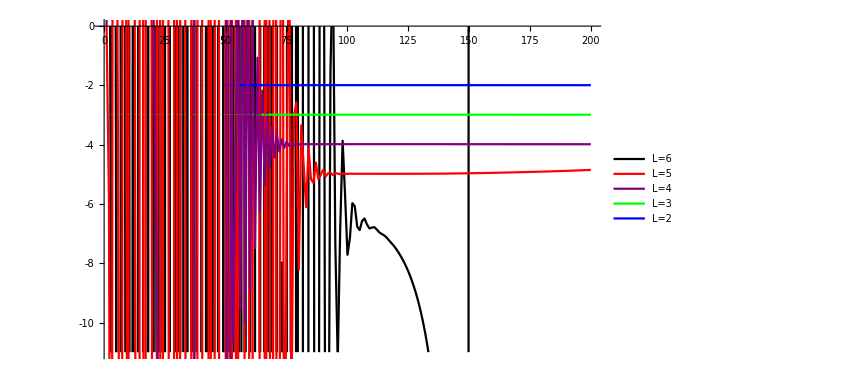

```mathematica
GridePosition=1;
listRepeatedS2=Table[ ConstantArray[0,tend],numberLmodes];
Do[
Do[listRepeatedS2[[j]][[i]]=tails[i,s2,j,GridePosition],
{i,2,tend}], {j,1,numberLmodes}
]
ListPlot[listRepeatedS2[[1]],Joined->True, PlotStyle->Blue, PlotLegends->{"L=2"}];
ListPlot[listRepeatedS2[[2]],Joined->True, PlotStyle->Green, PlotLegends->{"L=3"}];
ListPlot[listRepeatedS2[[3]],Joined->True, PlotStyle->Purple, PlotLegends->{"L=4"}];
ListPlot[listRepeatedS2[[4]],Joined->True, PlotStyle->Red, PlotLegends->{"L=5"}];
ListPlot[listRepeatedS2[[5]],Joined->True, PlotStyle->Black,PlotRange->{0,-11}, PlotLegends->{"L=6"},Ticks->{ Automatic,-Range[0,10,1]}];
Show[%,%%,%%%, %%%%,%%%%%]
```

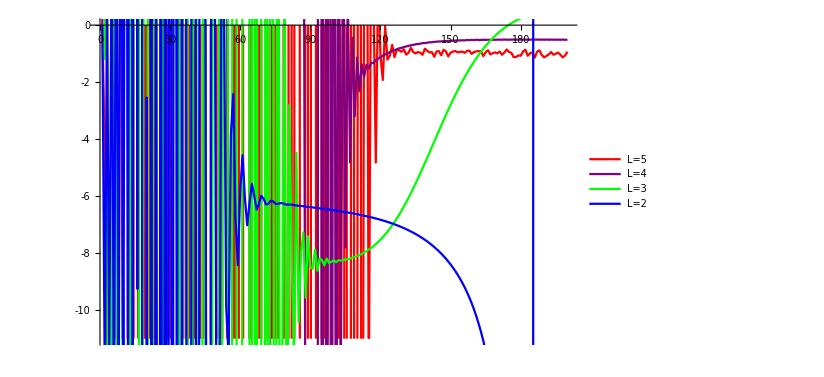

```mathematica
GridePosition=50;
listRepeatedS2=Table[ ConstantArray[0,tend],numberLmodes];
Do[
Do[listRepeatedS2[[j]][[i]]=tails[i,s2,j,GridePosition],
{i,2,tend}], {j,1,numberLmodes}
]
ListPlot[listRepeatedS2[[1]],Joined->True, PlotStyle->Blue, PlotLegends->{"L=2"}];
ListPlot[listRepeatedS2[[2]],Joined->True, PlotStyle->Green, PlotLegends->{"L=3"}];
ListPlot[listRepeatedS2[[3]],Joined->True, PlotStyle->Purple, PlotLegends->{"L=4"}];
ListPlot[listRepeatedS2[[4]],Joined->True, PlotStyle->Red,PlotRange->{0,-11}, PlotLegends->{"L=5"},Ticks->{ Automatic,-Range[0,10,1]}];
Show[%,%%,%%%, %%%%]
```

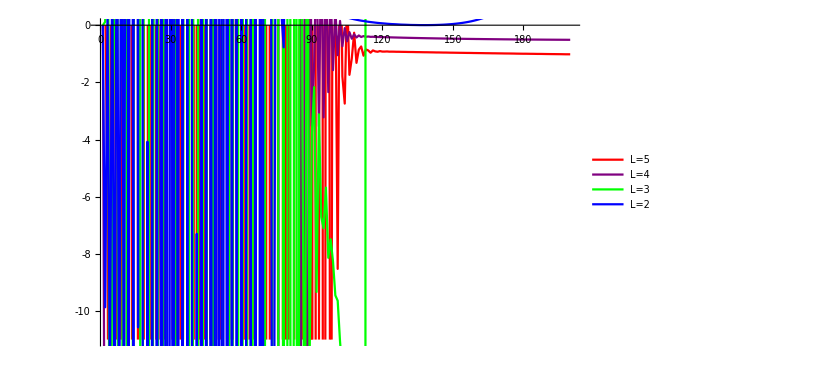

```mathematica
GridePosition=100;
listRepeatedS2=Table[ ConstantArray[0,tend],numberLmodes];
Do[
Do[listRepeatedS2[[j]][[i]]=tails[i,s2,j,GridePosition],
{i,2,tend}], {j,1,numberLmodes}
]
ListPlot[listRepeatedS2[[1]],Joined->True, PlotStyle->Blue, PlotLegends->{"L=2"}];
ListPlot[listRepeatedS2[[2]],Joined->True, PlotStyle->Green, PlotLegends->{"L=3"}];
ListPlot[listRepeatedS2[[3]],Joined->True, PlotStyle->Purple, PlotLegends->{"L=4"}];
ListPlot[listRepeatedS2[[4]],Joined->True, PlotStyle->Red,PlotRange->{0,-11}, PlotLegends->{"L=5"},Ticks->{ Automatic,-Range[0,10,1]},Ticks->{ Automatic,-Range[0,10,1]}];
Show[%,%%,%%%, %%%%]
```

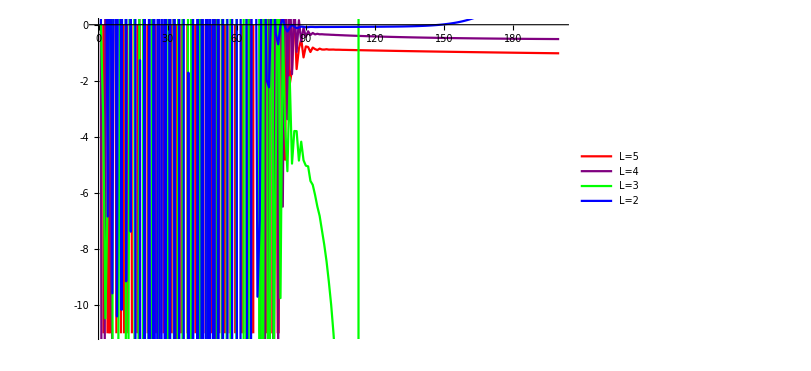

```mathematica
GridePosition=256;
listRepeatedS2=Table[ ConstantArray[0,tend],numberLmodes];
Do[
Do[listRepeatedS2[[j]][[i]]=tails[i,s2,j,GridePosition],
{i,2,tend}], {j,1,numberLmodes}
]
ListPlot[listRepeatedS2[[1]],Joined->True, PlotStyle->Blue, PlotLegends->{"L=2"}];
ListPlot[listRepeatedS2[[2]],Joined->True, PlotStyle->Green, PlotLegends->{"L=3"}];
ListPlot[listRepeatedS2[[3]],Joined->True, PlotStyle->Purple, PlotLegends->{"L=4"}];
ListPlot[listRepeatedS2[[4]],Joined->True, PlotStyle->Red,PlotRange->{0,-11}, PlotLegends->{"L=5"},Ticks->{ Automatic,-Range[0,10,1]}];
Show[%,%%,%%%, %%%%]
```

Kerr

S=0

```mathematica
s0Kerr = Import["C:\\Users\\brays\\PHD_CodeWork\\Data\\S=0.m.gz"];
```

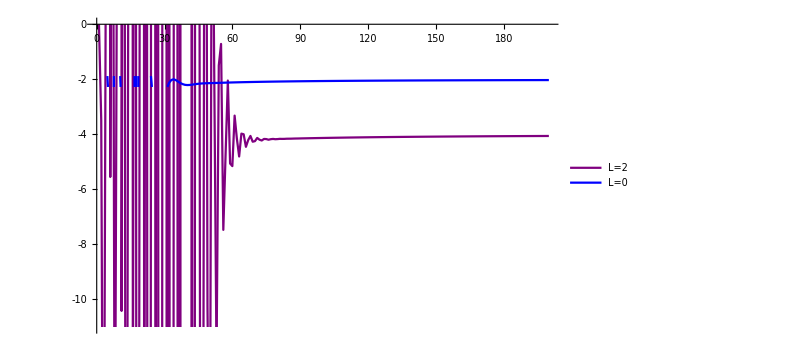

```mathematica
GridePosition=1;
listRepeatedKerrS0=Table[ ConstantArray[0,tend],numberLmodes];

Do[listRepeatedKerrS0[[1]][[i]]=tails[i,s0Kerr,1,GridePosition],
{i,2,tend}]

Do[listRepeatedKerrS0[[2]][[i]]=tails[i,s0Kerr,3,GridePosition],
{i,2,tend}]

ListPlot[listRepeatedKerrS0[[1]],Joined->True, PlotStyle->Blue, PlotLegends->{"L=0"}];
ListPlot[listRepeatedKerrS0[[2]],Joined->True, PlotStyle->Purple,PlotRange->{0,-11}, PlotLegends->{"L=2"},Ticks->{ Automatic,-Range[0,10,1]}];
Show[%,%%]
```

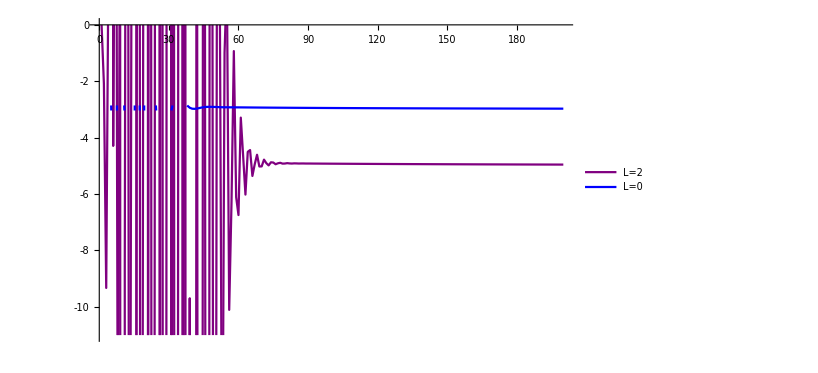

```mathematica
GridePosition=50;
listRepeatedKerrS0=Table[ ConstantArray[0,tend],numberLmodes];

Do[listRepeatedKerrS0[[1]][[i]]=tails[i,s0Kerr,1,GridePosition],
{i,2,tend}]

Do[listRepeatedKerrS0[[2]][[i]]=tails[i,s0Kerr,3,GridePosition],
{i,2,tend}]

ListPlot[listRepeatedKerrS0[[1]],Joined->True, PlotStyle->Blue, PlotLegends->{"L=0"}];
ListPlot[listRepeatedKerrS0[[2]],Joined->True, PlotStyle->Purple,PlotRange->{0,-11}, PlotLegends->{"L=2"},Ticks->{ Automatic,-Range[0,10,1]}];
Show[%,%%]
```

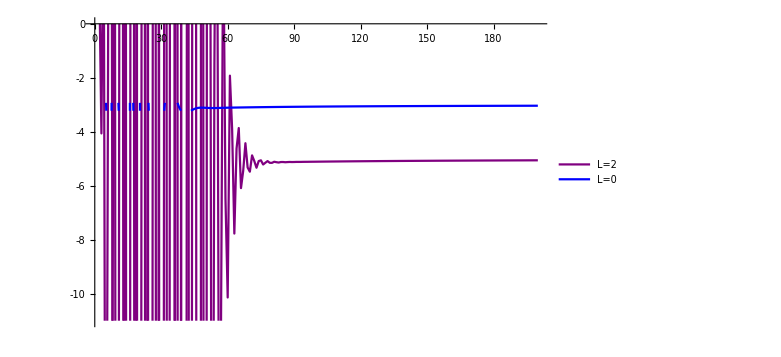

```mathematica
GridePosition=100;
listRepeatedKerrS0=Table[ ConstantArray[0,tend],numberLmodes];

Do[listRepeatedKerrS0[[1]][[i]]=tails[i,s0Kerr,1,GridePosition],
{i,2,tend}]

Do[listRepeatedKerrS0[[2]][[i]]=tails[i,s0Kerr,3,GridePosition],
{i,2,tend}]

ListPlot[listRepeatedKerrS0[[1]],Joined->True, PlotStyle->Blue, PlotLegends->{"L=0"}];
ListPlot[listRepeatedKerrS0[[2]],Joined->True, PlotStyle->Purple,PlotRange->{0,-11}, PlotLegends->{"L=2"},Ticks->{ Automatic,-Range[0,10,1]}];
Show[%,%%]
```

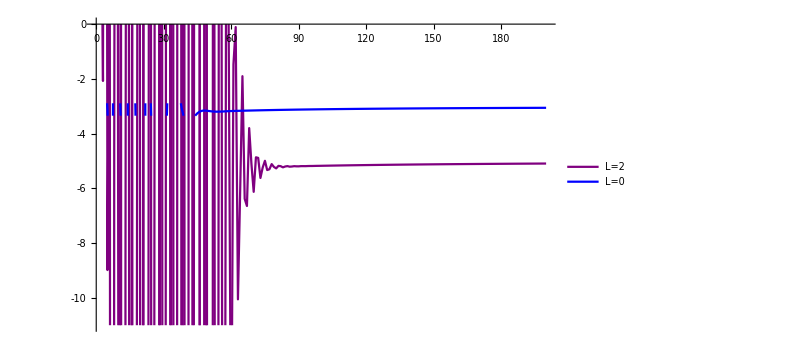

```mathematica
GridePosition=256;
listRepeatedKerrS0=Table[ ConstantArray[0,tend],numberLmodes];

Do[listRepeatedKerrS0[[1]][[i]]=tails[i,s0Kerr,1,GridePosition],
{i,2,tend}]

Do[listRepeatedKerrS0[[2]][[i]]=tails[i,s0Kerr,3,GridePosition],
{i,2,tend}]

ListPlot[listRepeatedKerrS0[[1]],Joined->True, PlotStyle->Blue, PlotLegends->{"L=0"}];
ListPlot[listRepeatedKerrS0[[2]],Joined->True, PlotStyle->Purple,PlotRange->{0,-11}, PlotLegends->{"L=2"},Ticks->{ Automatic,-Range[0,10,1]}];
Show[%,%%]
```

```mathematica
S=1
```

```mathematica
s1Kerr = Import["C:\\Users\\brays\\PHD_CodeWork\\Data\\S=1.m.gz"];
```

```mathematica
ListPlot[listRepeatedKerrS1[[3]],Joined->True, PlotStyle->Blue]
```

-Graphics-

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

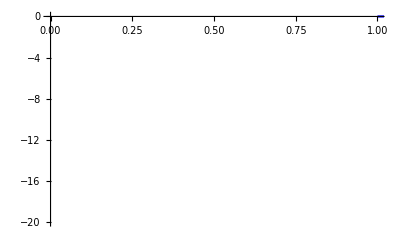

```mathematica
GridePosition=1;
listRepeatedKerrS1=Table[ ConstantArray[0,tend],numberLmodes];
Do[
Do[listRepeatedKerrS1[[j]][[i]]=tails[i,s1Kerr,j,GridePosition],
{i,2,tend}], {j,1,numberLmodes}
]
ListPlot[listRepeatedKerrS1[[1]],Joined->True, PlotStyle->Blue];
ListPlot[listRepeatedKerrS1[[2]],Joined->True, PlotStyle->Green];
ListPlot[listRepeatedKerrS1[[3]],Joined->True, PlotStyle->Purple];
ListPlot[listRepeatedKerrS1[[4]],Joined->True, PlotStyle->Red,PlotRange->{0,-20}];
Show[%,%%,%%%, %%%%]
```

```mathematica
S=2
```

(3 σ-σ^2/8) ψ_2[τ,σ]+σ (-2+2 (-2+σ)+(3-σ/4) σ) ψ_2^(0,1)[τ,σ]+σ^2 (-1+σ-σ^2/16) ψ_2^(0,2)[τ,σ]+(2 (-1+σ)+2 σ-1/16 σ (1+3 σ)) ψ_2^(1,0)[τ,σ]+(ⅈ ψ_3^(1,0)[τ,σ])/(2 √7)+(-1-σ^2 (-2+1/16 (1+2 σ))) ψ_2^(1,1)[τ,σ]+(3/14-(-1+σ/16) (1+σ)) ψ_2^(2,0)[τ,σ]-(ψ_4^(2,0)[τ,σ])/(14 √3)

(6+3 σ-σ^2/8) ψ_3[τ,σ]+σ (-2+2 (-2+σ)+(3-σ/4) σ) ψ_3^(0,1)[τ,σ]+σ^2 (-1+σ-σ^2/16) ψ_3^(0,2)[τ,σ]+(ⅈ ψ_2^(1,0)[τ,σ])/(2 √7)+(2 (-1+σ)+2 σ-1/16 σ (1+3 σ)) ψ_3^(1,0)[τ,σ]+(ⅈ ψ_4^(1,0)[τ,σ])/(√21)+(-1-σ^2 (-2+1/16 (1+2 σ))) ψ_3^(1,1)[τ,σ]+(1/6-(-1+σ/16) (1+σ)) ψ_3^(2,0)[τ,σ]-(ψ_5^(2,0)[τ,σ])/(6 √11)

(14+3 σ-σ^2/8) ψ_4[τ,σ]+σ (-2+2 (-2+σ)+(3-σ/4) σ) ψ_4^(0,1)[τ,σ]+σ^2 (-1+σ-σ^2/16) ψ_4^(0,2)[τ,σ]+(ⅈ ψ_3^(1,0)[τ,σ])/(√21)+(2 (-1+σ)+2 σ-1/16 σ (1+3 σ)) ψ_4^(1,0)[τ,σ]+1/2 ⅈ √(7/33) ψ_5^(1,0)[τ,σ]+(-1-σ^2 (-2+1/16 (1+2 σ))) ψ_4^(1,1)[τ,σ]-(ψ_2^(2,0)[τ,σ])/(14 √3)+(23/154-(-1+σ/16) (1+σ)) ψ_4^(2,0)[τ,σ]-1/11 √(14/39) ψ_6^(2,0)[τ,σ]

(24+3 σ-σ^2/8) ψ_5[τ,σ]+σ (-2+2 (-2+σ)+(3-σ/4) σ) ψ_5^(0,1)[τ,σ]+σ^2 (-1+σ-σ^2/16) ψ_5^(0,2)[τ,σ]+1/2 ⅈ √(7/33) ψ_4^(1,0)[τ,σ]+(2 (-1+σ)+2 σ-1/16 σ (1+3 σ)) ψ_5^(1,0)[τ,σ]+2 ⅈ √(2/143) ψ_6^(1,0)[τ,σ]+(-1-σ^2 (-2+1/16 (1+2 σ))) ψ_5^(1,1)[τ,σ]-(ψ_3^(2,0)[τ,σ])/(6 √11)+(11/78-(-1+σ/16) (1+σ)) ψ_5^(2,0)[τ,σ]-1/13 √(6/11) ψ_7^(2,0)[τ,σ]

```mathematica
s2Kerr = Import["C:\\Users\\brays\\PHD_CodeWork\\Data\\S=2.m.gz"];
```

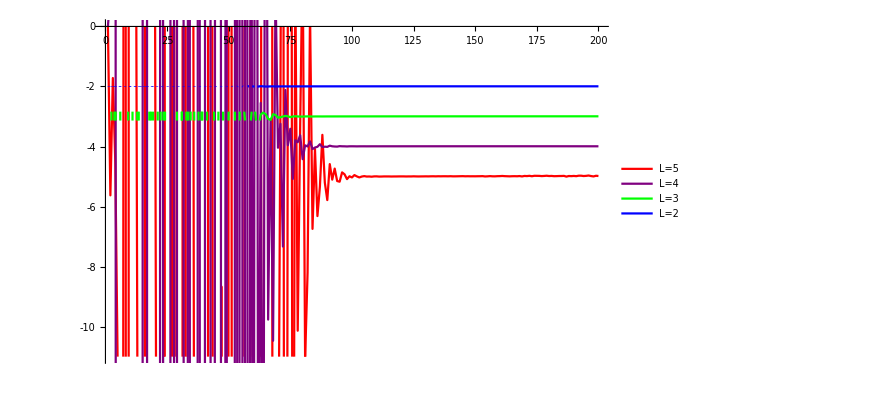

```mathematica
GridePosition=1;
listRepeatedKerrS2=Table[ ConstantArray[0,tend],numberLmodes];
Do[
Do[listRepeatedKerrS2[[j]][[i]]=tails[i,s2Kerr,j,GridePosition],
{i,2,tend}], {j,1,numberLmodes}
]
ListPlot[listRepeatedKerrS2[[1]],Joined->True, PlotStyle->Blue, PlotLegends->{"L=2"}];
ListPlot[listRepeatedKerrS2[[2]],Joined->True, PlotStyle->Green, PlotLegends->{"L=3"}];
ListPlot[listRepeatedKerrS2[[3]],Joined->True, PlotStyle->Purple, PlotLegends->{"L=4"}];
ListPlot[listRepeatedKerrS2[[4]],Joined->True, PlotStyle->Red,PlotRange->{0,-11}, PlotLegends->{"L=5"},Ticks->{ Automatic,-Range[0,10,1]}];
Show[%,%%,%%%, %%%%]
```

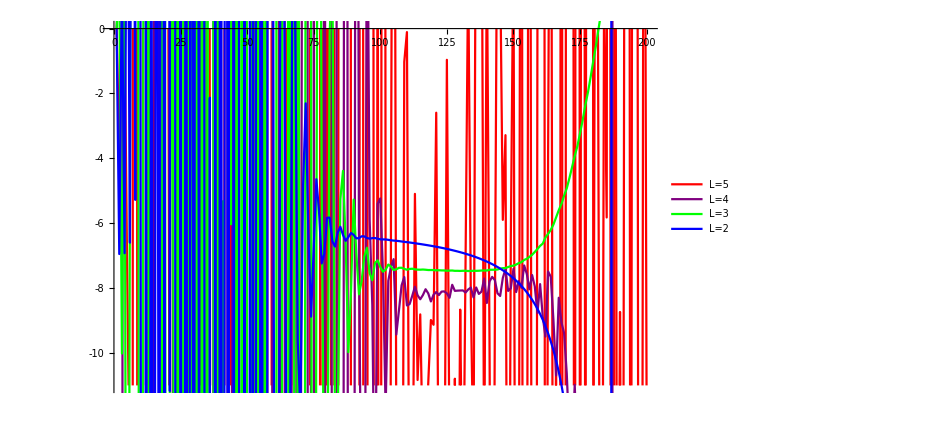

```mathematica
GridePosition=50;
listRepeatedKerrS2=Table[ ConstantArray[0,tend],numberLmodes];
Do[
Do[listRepeatedKerrS2[[j]][[i]]=tails[i,s2Kerr,j,GridePosition],
{i,2,tend}], {j,1,numberLmodes}
]
ListPlot[listRepeatedKerrS2[[1]],Joined->True, PlotStyle->Blue, PlotLegends->{"L=2"}];
ListPlot[listRepeatedKerrS2[[2]],Joined->True, PlotStyle->Green, PlotLegends->{"L=3"}];
ListPlot[listRepeatedKerrS2[[3]],Joined->True, PlotStyle->Purple, PlotLegends->{"L=4"}];
ListPlot[listRepeatedKerrS2[[4]],Joined->True, PlotStyle->Red,PlotRange->{0,-11}, PlotLegends->{"L=5"},Ticks->{ Automatic,-Range[0,10,1]}];
Show[%,%%,%%%, %%%%]
```

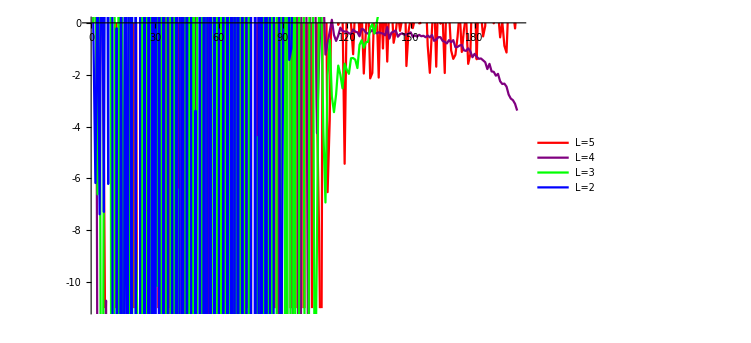

```mathematica
GridePosition=100;
listRepeatedKerrS2=Table[ ConstantArray[0,tend],numberLmodes];
Do[
Do[listRepeatedKerrS2[[j]][[i]]=tails[i,s2Kerr,j,GridePosition],
{i,2,tend}], {j,1,numberLmodes}
]
ListPlot[listRepeatedKerrS2[[1]],Joined->True, PlotStyle->Blue, PlotLegends->{"L=2"}];
ListPlot[listRepeatedKerrS2[[2]],Joined->True, PlotStyle->Green, PlotLegends->{"L=3"}];
ListPlot[listRepeatedKerrS2[[3]],Joined->True, PlotStyle->Purple, PlotLegends->{"L=4"}];
ListPlot[listRepeatedKerrS2[[4]],Joined->True, PlotStyle->Red,PlotRange->{0,-11}, PlotLegends->{"L=5"},Ticks->{ Automatic,-Range[0,10,1]}];
Show[%,%%,%%%, %%%%]
```

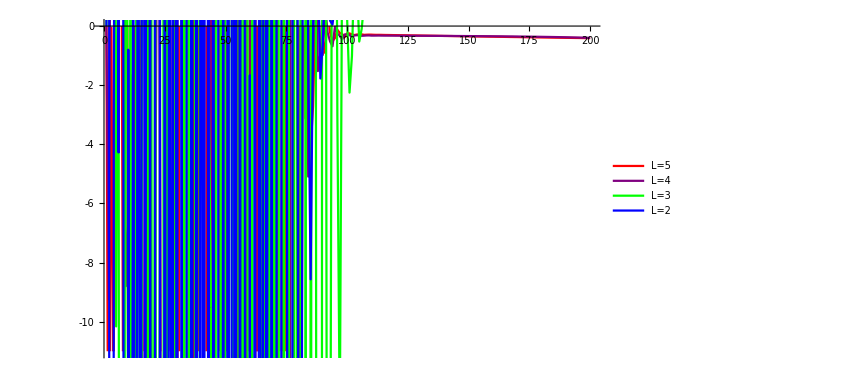

```mathematica
GridePosition=256;
listRepeatedKerrS2=Table[ ConstantArray[0,tend],numberLmodes];
Do[
Do[listRepeatedKerrS2[[j]][[i]]=tails[i,s2Kerr,j,GridePosition],
{i,2,tend}], {j,1,numberLmodes}
]
ListPlot[listRepeatedKerrS2[[1]],Joined->True, PlotStyle->Blue, PlotLegends->{"L=2"}];
ListPlot[listRepeatedKerrS2[[2]],Joined->True, PlotStyle->Green, PlotLegends->{"L=3"}];
ListPlot[listRepeatedKerrS2[[3]],Joined->True, PlotStyle->Purple, PlotLegends->{"L=4"}];
ListPlot[listRepeatedKerrS2[[4]],Joined->True, PlotStyle->Red,PlotRange->{0,-11}, PlotLegends->{"L=5"},Ticks->{ Automatic,-Range[0,10,1]}];
Show[%,%%,%%%, %%%%]
```